Kyungwon Chun

```mathematica
DateString[]
$Version
<<SymbolicComputing`
$SCVersion
```

## References

W. E. Boyce and R. C. DiPrima, Elementary Differential Equations and Boundary Value Problems, 10th ed. Wiley, 2012.

## Separation of Variables; Heat Conduction

-Graphics-

```mathematica
α^2(∂^2 u)/(∂x^2)==(∂u)/(∂t)(*eq1*)
SCMAF[%,RA,{All,u==X[x]T[t]},Post->SCEvalDeriv,
SCDivEq,{All,α^2 X[x]T[t]},Post->SCAbbrevFunc](*eq7*)
```

α^2 (∂^2 u)/(∂x^2)==(∂u)/(∂t)

α^2 T[t] X''[x]==X[x] T'[t]

X''/X==T'/(T α^2)

It is necessary that both sides of Eq. 7 be equal to the same constant, -σ.

```mathematica
{X''/X==-σ,T'/(T α^2)==-σ}
SCMAF[%,FullSimplify,All,
SCMultEq,{{At[1],X},{At[2],T α^2}}](*eq9,eq10*)
```

{X''/X==-σ,T'/(T α^2)==-σ}

{σ+X''/X==0,σ+T'/(T α^2)==0}

{X σ+X''==0,T α^2 σ+T'==0}

If σ=0.

```mathematica
X σ+X''==0
SCMAF[%,RA,{At[1],σ==0},
SCDSolve,{All,X,x,ReplConst->{Subscript[k, 1],Subscript[k, 2]}}]
```

X σ+X''==0

X''==0

X==k_1+x k_2

```mathematica
{X[0]==0,X[L]==0}(*eq4*)
SCMAF[%,RA,{All,X[x_]==Subscript[k, 1]+x Subscript[k, 2]},
SCSolve,{All,{Subscript[k, 1],Subscript[k, 2]}}]
```

{X[0]==0,X[L]==0}

{k_1==0,k_1+L k_2==0}

{k_1==0,k_2==0}

Only, a trivial solution exists.

If σ<0, let σ=-λ^2 where λ>0.

```mathematica
X σ+X''==0
SCMAF[%,RA,{At[1],σ==-λ^2(*λ>0*)},
SCDSolve,{All,X,x,}]
```

X σ+X''==0

-X λ^2+X''==0

X==ⅇ^(x λ) C[1]+ⅇ^(-x λ) C[2]

```mathematica
{X[0]==0,X[L]==0}(*eq4*)
SCMAF[%,RA,{All,X[x_]==ⅇ^(x λ) C[1]+ⅇ^(-x λ) C[2]},
SCSolve,{All,{C[1],C[2]}}]
```

{X[0]==0,X[L]==0}

{C[1]+C[2]==0,ⅇ^(L λ) C[1]+ⅇ^(-L λ) C[2]==0}

{C[1]==0,C[2]==0}

Also, a trivial solution is the only solution.

If σ>0, let σ=λ^2 where λ>0.

```mathematica
X σ+X''==0
SCMAF[%,RA,{At[1],σ==λ^2(*λ>0*)},
SCDSolve,{All,X,x,ReplConst->{Subscript[k, 1],Subscript[k, 2]}}]
```

X σ+X''==0

X λ^2+X''==0

X==Cos[x λ] k_1+Sin[x λ] k_2

```mathematica
{X[0]==0,X[L]==0}(*eq4*)
SCMAF[%,RA,{All,X[x_]==Cos[x λ] Subscript[k, 1]+Sin[x λ] Subscript[k, 2]}]
```

{X[0]==0,X[L]==0}

{k_1==0,Cos[L λ] k_1+Sin[L λ] k_2==0}

```mathematica
Cos[L λ] Subscript[k, 1]+Sin[L λ] Subscript[k, 2]==0
SCMAF[%,RA,{At[1],Subscript[k, 1]==0},
SCReduce,{All,λ},Post->FullSimplify]
```

Cos[L λ] k_1+Sin[L λ] k_2==0

Sin[L λ] k_2==0

(C[1]∈ℤ&&(L==0||λ==(2 π C[1])/L||λ==(π+2 π C[1])/L))||k_2==0

Thus, L λ=n π and

```mathematica
X==Cos[x λ] Subscript[k, 1]+Sin[x λ] Subscript[k, 2]
SCMAF[%,SCEliminate,{At[2],{Subscript[k, 1]==0,L λ==n π},{Subscript[k, 1],λ}}]
```

X==Cos[x λ] k_1+Sin[x λ] k_2

X==k_2 Sin[(n π x)/L]

If we substitute L into the Eq. 9,

```mathematica
X σ+X''==0(*eq9*)
SCMAF[%,SCAbbrevDeriv,{At[1],Functions->X[x]},
RA,{At[1],X==Subscript[k, 2] Sin[(n π x)/L]},Post->SCEvalDeriv,
SCSolve,{All,σ}](*eq23*)
```

X σ+X''==0

-(n^2 π^2 k_2)/L^2 Sin[(n π x)/L]+σ k_2 Sin[(n π x)/L]==0

σ==(n^2 π^2)/L^2

The values of σ given in Eq.(23), for which nontrivial solutions exist, are called eigenvalues of the boundary value problem. The corresponding nontrivial solutions X(x), which are proportional to sin(nπx/L), aare called eigenfuncitons.

Substituting for σ in Eq.(10),

```mathematica
T α^2 σ+T'==0(*eq10*)
SCMAF[%,RA,{At[1],σ==(n^2 π^2)/L^2(*eq23*)},
SCDSolve,{All,T,t}]
```

T α^2 σ+T'==0

(n^2 π^2 T α^2)/L^2+T'==0

T==ⅇ^(-(n^2 π^2 t α^2)/L^2) C[1]

The fundamental solutions is

```mathematica
Subscript[u, n][x,t]==Subscript[X, n][x]Subscript[T, n][t]
SCMAF[%,RA,{At[2],{ Subscript[X, n][x]== Sin[(n π x)/L],Subscript[T, n][t]==ⅇ^(-(n^2 π^2 t α^2)/L^2)}}](*eq17*)
```

u_n[x,t]==T_n[t] X_n[x]

u_n[x,t]==ⅇ^(-(n^2 π^2 t α^2)/L^2) Sin[(n π x)/L]

The general linear combination of the functions is

```mathematica
u[x,t]==∑_(n=1)^∞ Subscript[c, n] Subscript[u, n][x,t]
SCMAF[%,RA,{At[2],Subscript[u, n][x,t]==ⅇ^(-(n^2 π^2 t α^2)/L^2) Sin[(n π x)/L]}](*eq19*)
```

u[x,t]==∑_(n=1)^∞ c_n u_n[x,t]

u[x,t]==∑_(n=1)^∞ ⅇ^(-(n^2 π^2 t α^2)/L^2) c_n Sin[(n π x)/L]

To satisfy the initial condition,

```mathematica
u[x,t]==∑_(n=1)^∞ ⅇ^(-(n^2 π^2 t α^2)/L^2) Subscript[c, n] Sin[(n π x)/L]/.t->0
SCMAF[%,RA,{At[1],u[x,0]==f[x]}](*eq20*)
```

u[x,0]==∑_(n=1)^∞ c_n Sin[(n π x)/L]

f[x]==∑_(n=1)^∞ c_n Sin[(n π x)/L]

The coefficient c_n is given by

```mathematica
Subscript[c, n]==2/L∫_0^L f[x]Sin[(n π x)/L]ⅆx(*eq21*)
```

c_n==2/L ∫_0^L f[x] Sin[(n π x)/L]ⅆx

#### Example 1

```mathematica
u[x,t]==∑_(n=1)^∞ ⅇ^(-(n^2 π^2 t α^2)/L^2) Subscript[c, n] Sin[(n π x)/L](*eq19*)/.L->50(*eq22*)
```

u[x,t]==∑_(n=1)^∞ ⅇ^(-(n^2 π^2 t α^2)/2500) c_n Sin[(n π x)/50]

```mathematica
Subscript[c, n]==2/L∫_0^L f[x]Sin[(n π x)/L]ⅆx(*eq21*)
SCMAF[%,RA,{At[2],{f[x]==20,L==50}},Post->SCEvalInt,
FullSimplify,{At[2],n>0&&n∈Integers}](*eq23*)
```

c_n==2/L ∫_0^L f[x] Sin[(n π x)/L]ⅆx

c_n==-(40 (-1+Cos[n π]))/(n π)

c_n==-(40 (-1+(-1)^n))/(n π)

```mathematica
u[x,t]==∑_(n=1)^∞ ⅇ^(-(n^2 π^2 t α^2)/2500) Subscript[c, n] Sin[(n π x)/50]
SCMAF[%,RA,{At[2],Subscript[c, n]==-(40 (-1+(-1)^n))/(n π)},Post->FullSimplify](*eq24*)
```

u[x,t]==∑_(n=1)^∞ ⅇ^(-(n^2 π^2 t α^2)/2500) c_n Sin[(n π x)/50]

u[x,t]==-40/π ∑_(n=1)^∞ ((-1+(-1)^n) ⅇ^(-(n^2 π^2 t α^2)/2500))/n Sin[(n π x)/50]

Temperature distribution at several times is

{u[x,0],u[x,20],u[x,50],u[x,150],u[x,300]}=={-40/π ∑_(n=1)^∞ (-1+(-1)^n)/n Sin[(n π x)/50],-40/π ∑_(n=1)^∞ ((-1+(-1)^n) ⅇ^(-1/125 n^2 π^2))/n Sin[(n π x)/50],-40/π ∑_(n=1)^∞ ((-1+(-1)^n) ⅇ^(-1/50 n^2 π^2))/n Sin[(n π x)/50],-40/π ∑_(n=1)^∞ ((-1+(-1)^n) ⅇ^(-3/50 n^2 π^2))/n Sin[(n π x)/50],-40/π ∑_(n=1)^∞ ((-1+(-1)^n) ⅇ^(-3/25 n^2 π^2))/n Sin[(n π x)/50]}

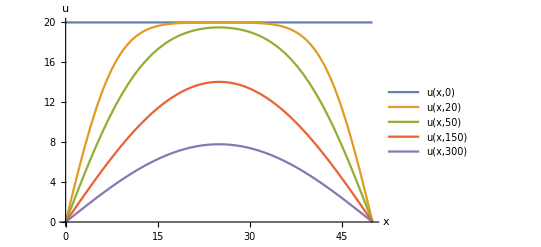

```mathematica
SCARR[{u[x,0],u[x,20],u[x,50],u[x,150],u[x,300]},
{u[x_,t_]==-40/π ∑_(n=1)^∞ ((-1+(-1)^n) ⅇ^(-(n^2 π^2 t α^2)/2500))/n Sin[(n π x)/50](*eq24*),α^2==1},
SCEvalSum,{At[2,1]},
SCSumChangeInterval,{At[2],{n,1,100}},Post->SCEvalSum,,,,
Plot,{At[2],{x,0,50},AxesLabel->{x,u},PlotLegends->At[1]},Take->{2},IgnoreError->True]
```

Dependence of temperature on time at several locations,

{u[5,t],u[15,t],u[25,t]}=={-40/π ∑_(n=1)^∞ ((-1+(-1)^n) ⅇ^(-(n^2 π^2 t)/2500))/n Sin[(n π)/10],-40/π ∑_(n=1)^∞ ((-1+(-1)^n) ⅇ^(-(n^2 π^2 t)/2500))/n Sin[(3 n π)/10],-40/π ∑_(n=1)^∞ ((-1+(-1)^n) ⅇ^(-(n^2 π^2 t)/2500))/n Sin[(n π)/2]}

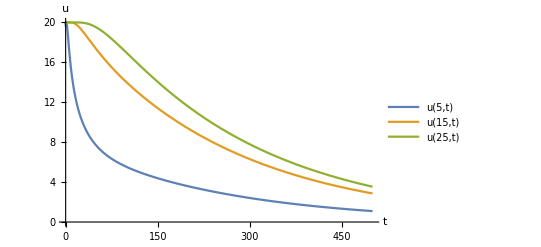

```mathematica
SCARR[{u[5,t],u[15,t],u[25,t]},
{u[x_,t_]==-40/π ∑_(n=1)^∞ ((-1+(-1)^n) ⅇ^(-(n^2 π^2 t α^2)/2500))/n Sin[(n π x)/50](*eq24*),α^2==1},
SCSumChangeInterval,{At[2],{n,1,100}},Post->SCEvalSum,,,,
Plot,{At[2],{t,0,500},AxesLabel->{t,u},PlotLegends->At[1]},Take->{2}]
```

A plot of temperature u versus x and t is

```mathematica
u[x,t]==-40/π ∑_(n=1)^∞ ((-1+(-1)^n) ⅇ^(-(n^2 π^2 t α^2)/2500))/n Sin[(n π x)/50](*eq24*)
SCMAF[%,RA,{At[2],α^2==1},
SCSumChangeInterval,{At[2],{n,1,100}},Post->SCEvalSum,,,,
Plot3D,{At[2],{x,0,50},{t,0,250},AxesLabel->{x,t,u},PlotStyle->Opacity[0.5]},Take->{2}]
```

u[x,t]==-40/π ∑_(n=1)^∞ ((-1+(-1)^n) ⅇ^(-(n^2 π^2 t α^2)/2500))/n Sin[(n π x)/50]

-Graphics3D-